### Flow of complexity

```mathematica
NewBCompression2DArrowed[x_List,width_Integer,separatordots_:True]:=Module[{fx=Flatten[x[[1]]],fy=(Flatten[#1/.{Separator->2,Labeled[u_,v_]->u,Dotted[u_,v_,w___]:>With[{z=If[{w}==={},{-1},w]},Table[If[MemberQ[z,i]||MemberQ[z,i-Length[u]-1],Dotted[u[[i]]],u[[i]]],{i,Length[u]}]],Arrowed[u_,v_,w___]:>With[{z=If[{w}==={},{1},w]},Table[If[MemberQ[z,i]||MemberQ[z,i-Length[u]-1],Arrowed[u[[i]]],u[[i]]],{i,Length[u]}]]}]&)/@Rest[x],ii,jj},GraphicsRow[Insert[Graphics[{ii=0;jj=0;Table[{ii++;If[ii>width,ii=1;jj--];GrayLevel[Switch[If[IntegerQ[#1[[i]]],#1[[i]],#1[[i,1]]],0,0.85,1,0,2,0.5]],Rectangle[{ii-1,jj-1},{ii,jj}],If[separatordots&&#1[[i]]===2,{GrayLevel[0],Disk[{ii-0.5,jj-0.5},.125]},If[Head[#1[[i]]]===Dotted,{Gray,Disk[{ii-0.5,jj-0.5},.35]},If[Head[#1[[i]]]===Arrowed,{GrayLevel[0.5],Polygon[{{ii-0.6,jj-0.2},{ii-0.6,jj-0.8},{ii-0.3,jj-0.5}}]},{}]]],Directive[GrayLevel[0.15],AbsoluteThickness[0.25]],Line[{{ii-1,jj-1},{ii-1,jj},{ii,jj},{ii,jj-1},{ii-1,jj-1}}]},{i,Length[#1]}]},ImageSize->200]&/@Prepend[fy,fx],Graphics[{Arrowheads[Small],Arrow[{{0,0},{1,0}}]},ImageSize->20],2]]]

frequencyData[data_]:=Sort[Function[α,Transpose[{α,(Count[data,#]&/@α)/Length[data]}]][Union[data]],Last[#1]>Last[#2]&]

merge[data_]:=If[Length[data]>1,{{{#1[[1]],#2[[1]]},#1[[2]]+#2[[2]]},##3}&@@Sort[data,#1[[2]]<#2[[2]]&],data]

mergeAll[data_]:=If[Length[data]>1,FixedPoint[merge,data][[1,1]],{data[[1,1]]}]

HuffmanTree[data_,b_]:=mergeAll[frequencyData[Partition[data,b]]]

HassignCode[data_,l_]:=Flatten[MapIndexed[(#1->Mod[#2+1,2])&,data,{-l}]]

HgenerateCode[data_]:=HassignCode[mergeAll[frequencyData[data]],Depth[data[[1]]]]

HuffmanEncode[data_,b_]:=Module[{data1=Partition[data,b],code},code=HgenerateCode[data1];{code,Flatten[data1/.code]}]

HuffmanCodeBlock[data_,s_,lm_]:=Flatten[Module[{f,g,ct=1},(Apply[f,HuffmanTree[data,s],{-2}]/.List->g)//.{g[a_,b_]:>{Arrowed[{0},""],a,b},f[x__]:>{Arrowed[{1},""],Labeled[{x},{x}/.lm]}}]]

DiagramHuffmanEncode[data_,b_]:=Module[{c=First[HuffmanEncode[data,b]],d,fd,lm},lm=MapIndexed[#->First[#2]&,Last/@Reverse[Sort[Reverse/@frequencyData[Partition[data,b]]]]];
{Prepend[Partition[data,b],{}],Join[{HuffmanCodeBlock[data,b,lm]},List/@MapThread[Dotted,{Partition[data,b]/.c,Partition[data,b]/.lm}]]}]

GraphicsGrid[Partition[NewBCompression2DArrowed[DiagramHuffmanEncode[#1,6],51]&/@Join[Flatten[CellularAutomaton[#1,CenterArray[{1},51],25]]&/@{254,250,90,150,30},Flatten[Take[#1,{27,-27}]&/@Drop[CellularAutomaton[#1,CenterArray[{1},103],50],25]]&/@{30}],2],ImageSize->700]
```

$Aborted

```mathematica
DiagramHuffmanEncode[CellularAutomaton[254,CenterArray[{1},51],25][[1]], 3][[1]]
```

{{},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,1,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}

```mathematica
CellularAutomaton[254,CenterArray[{1},51],25][[1]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
DiagramHuffmanEncode[#1,6]&/@CellularAutomaton[254,CenterArray[{1},51],25]
```

{{{{},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,1,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}},{{Arrowed[{0},],Arrowed[{1},],{0,1,0,0,0,0}2,Arrowed[{1},],{0,0,0,0,0,0}1},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{0},2]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]}}},{{{},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{1,1,1,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}},{{Arrowed[{0},],Arrowed[{1},],{1,1,1,0,0,0}2,Arrowed[{1},],{0,0,0,0,0,0}1},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{0},2]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]}}},{{{},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,1},{1,1,1,1,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}},{{Arrowed[{0},],Arrowed[{0},],Arrowed[{1},],{0,0,0,0,0,1}3,Arrowed[{1},],{1,1,1,1,0,0}2,Arrowed[{1},],{0,0,0,0,0,0}1},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{0,0},3]},{Dashing[{0,Small}][{0,1},2]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]}}},{{{},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,1,1},{1,1,1,1,1,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}},{{Arrowed[{0},],Arrowed[{0},],Arrowed[{1},],{0,0,0,0,1,1}3,Arrowed[{1},],{1,1,1,1,1,0}2,Arrowed[{1},],{0,0,0,0,0,0}1},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{0,0},3]},{Dashing[{0,Small}][{0,1},2]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]}}},{{{},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,1,1,1},{1,1,1,1,1,1},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}},{{Arrowed[{0},],Arrowed[{0},],Arrowed[{1},],{0,0,0,1,1,1}3,Arrowed[{1},],{1,1,1,1,1,1}2,Arrowed[{1},],{0,0,0,0,0,0}1},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{0,0},3]},{Dashing[{0,Small}][{0,1},2]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]}}},{{{},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,1,1,1,1},{1,1,1,1,1,1},{1,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}},{{Arrowed[{0},],Arrowed[{0},],Arrowed[{1},],{1,1,1,1,1,1}2,Arrowed[{0},],Arrowed[{1},],{0,0,1,1,1,1}4,Arrowed[{1},],{1,0,0,0,0,0}3,Arrowed[{1},],{0,0,0,0,0,0}1},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{0,1,0},4]},{Dashing[{0,Small}][{0,0},2]},{Dashing[{0,Small}][{0,1,1},3]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]}}},{{{},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,1,1,1,1,1},{1,1,1,1,1,1},{1,1,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}},{{Arrowed[{0},],Arrowed[{0},],Arrowed[{1},],{1,1,1,1,1,1}2,Arrowed[{0},],Arrowed[{1},],{0,1,1,1,1,1}4,Arrowed[{1},],{1,1,0,0,0,0}3,Arrowed[{1},],{0,0,0,0,0,0}1},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{0,1,0},4]},{Dashing[{0,Small}][{0,0},2]},{Dashing[{0,Small}][{0,1,1},3]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]}}},{{{},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}},{{Arrowed[{0},],Arrowed[{0},],Arrowed[{1},],{1,1,1,0,0,0}3,Arrowed[{1},],{1,1,1,1,1,1}2,Arrowed[{1},],{0,0,0,0,0,0}1},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{0,1},2]},{Dashing[{0,Small}][{0,1},2]},{Dashing[{0,Small}][{0,0},3]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]}}},{{{},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}},{{Arrowed[{0},],Arrowed[{1},],{0,0,0,0,0,0}1,Arrowed[{0},],Arrowed[{1},],{1,1,1,1,1,1}2,Arrowed[{0},],Arrowed[{1},],{0,0,0,0,0,1}4,Arrowed[{1},],{1,1,1,1,0,0}3},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{1,1,0},4]},{Dashing[{0,Small}][{1,0},2]},{Dashing[{0,Small}][{1,0},2]},{Dashing[{0,Small}][{1,1,1},3]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]}}},{{{},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,0},{0,0,0,0,0,0},{0,0,0,0,0,0}},{{Arrowed[{0},],Arrowed[{1},],{0,0,0,0,0,0}1,Arrowed[{0},],Arrowed[{1},],{1,1,1,1,1,1}2,Arrowed[{0},],Arrowed[{1},],{0,0,0,0,1,1}4,Arrowed[{1},],{1,1,1,1,1,0}3},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{1,1,0},4]},{Dashing[{0,Small}][{1,0},2]},{Dashing[{0,Small}][{1,0},2]},{Dashing[{0,Small}][{1,1,1},3]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]}}},{{{},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{0,0,0,0,0,0},{0,0,0,0,0,0}},{{Arrowed[{0},],Arrowed[{1},],{0,0,0,0,0,0}1,Arrowed[{0},],Arrowed[{1},],{0,0,0,1,1,1}3,Arrowed[{1},],{1,1,1,1,1,1}2},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{1,0},3]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]}}},{{{},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,0,0,0,0,0},{0,0,0,0,0,0}},{{Arrowed[{0},],Arrowed[{1},],{0,0,0,0,0,0}2,Arrowed[{0},],Arrowed[{0},],Arrowed[{1},],{0,0,1,1,1,1}4,Arrowed[{1},],{1,0,0,0,0,0}3,Arrowed[{1},],{1,1,1,1,1,1}1},{Dashing[{0,Small}][{0},2]},{Dashing[{0,Small}][{0},2]},{Dashing[{0,Small}][{1,0,0},4]},{Dashing[{0,Small}][{1,1},1]},{Dashing[{0,Small}][{1,1},1]},{Dashing[{0,Small}][{1,1},1]},{Dashing[{0,Small}][{1,0,1},3]},{Dashing[{0,Small}][{0},2]}}},{{{},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,0,0,0,0},{0,0,0,0,0,0}},{{Arrowed[{0},],Arrowed[{1},],{0,0,0,0,0,0}2,Arrowed[{0},],Arrowed[{0},],Arrowed[{1},],{0,1,1,1,1,1}4,Arrowed[{1},],{1,1,0,0,0,0}3,Arrowed[{1},],{1,1,1,1,1,1}1},{Dashing[{0,Small}][{0},2]},{Dashing[{0,Small}][{0},2]},{Dashing[{0,Small}][{1,0,0},4]},{Dashing[{0,Small}][{1,1},1]},{Dashing[{0,Small}][{1,1},1]},{Dashing[{0,Small}][{1,1},1]},{Dashing[{0,Small}][{1,0,1},3]},{Dashing[{0,Small}][{0},2]}}},{{{},{0,0,0,0,0,0},{0,0,0,0,0,0},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,0,0,0},{0,0,0,0,0,0}},{{Arrowed[{0},],Arrowed[{1},],{1,1,1,1,1,1}1,Arrowed[{0},],Arrowed[{1},],{1,1,1,0,0,0}3,Arrowed[{1},],{0,0,0,0,0,0}2},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{1,0},3]},{Dashing[{0,Small}][{1,1},2]}}},{{{},{0,0,0,0,0,0},{0,0,0,0,0,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,0,0},{0,0,0,0,0,0}},{{Arrowed[{0},],Arrowed[{1},],{1,1,1,1,1,1}1,Arrowed[{0},],Arrowed[{1},],{0,0,0,0,0,0}2,Arrowed[{0},],Arrowed[{1},],{0,0,0,0,0,1}4,Arrowed[{1},],{1,1,1,1,0,0}3},{Dashing[{0,Small}][{1,0},2]},{Dashing[{0,Small}][{1,1,0},4]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{1,1,1},3]},{Dashing[{0,Small}][{1,0},2]}}},{{{},{0,0,0,0,0,0},{0,0,0,0,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,0},{0,0,0,0,0,0}},{{Arrowed[{0},],Arrowed[{1},],{1,1,1,1,1,1}1,Arrowed[{0},],Arrowed[{1},],{0,0,0,0,0,0}2,Arrowed[{0},],Arrowed[{1},],{0,0,0,0,1,1}4,Arrowed[{1},],{1,1,1,1,1,0}3},{Dashing[{0,Small}][{1,0},2]},{Dashing[{0,Small}][{1,1,0},4]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{1,1,1},3]},{Dashing[{0,Small}][{1,0},2]}}},{{{},{0,0,0,0,0,0},{0,0,0,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{0,0,0,0,0,0}},{{Arrowed[{0},],Arrowed[{0},],Arrowed[{1},],{0,0,0,1,1,1}3,Arrowed[{1},],{0,0,0,0,0,0}2,Arrowed[{1},],{1,1,1,1,1,1}1},{Dashing[{0,Small}][{0,1},2]},{Dashing[{0,Small}][{0,0},3]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{0,1},2]}}},{{{},{0,0,0,0,0,0},{0,0,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,0,0,0,0,0}},{{Arrowed[{0},],Arrowed[{0},],Arrowed[{1},],{1,0,0,0,0,0}2,Arrowed[{0},],Arrowed[{1},],{0,0,0,0,0,0}4,Arrowed[{1},],{0,0,1,1,1,1}3,Arrowed[{1},],{1,1,1,1,1,1}1},{Dashing[{0,Small}][{0,1,0},4]},{Dashing[{0,Small}][{0,1,1},3]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{0,0},2]}}},{{{},{0,0,0,0,0,0},{0,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,0,0,0,0}},{{Arrowed[{0},],Arrowed[{0},],Arrowed[{1},],{1,1,0,0,0,0}2,Arrowed[{0},],Arrowed[{1},],{0,0,0,0,0,0}4,Arrowed[{1},],{0,1,1,1,1,1}3,Arrowed[{1},],{1,1,1,1,1,1}1},{Dashing[{0,Small}][{0,1,0},4]},{Dashing[{0,Small}][{0,1,1},3]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{0,0},2]}}},{{{},{0,0,0,0,0,0},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,0,0,0}},{{Arrowed[{0},],Arrowed[{0},],Arrowed[{1},],{0,0,0,0,0,0}3,Arrowed[{1},],{1,1,1,0,0,0}2,Arrowed[{1},],{1,1,1,1,1,1}1},{Dashing[{0,Small}][{0,0},3]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{0,1},2]}}},{{{},{0,0,0,0,0,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,0,0}},{{Arrowed[{0},],Arrowed[{0},],Arrowed[{1},],{0,0,0,0,0,1}3,Arrowed[{1},],{1,1,1,1,0,0}2,Arrowed[{1},],{1,1,1,1,1,1}1},{Dashing[{0,Small}][{0,0},3]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{0,1},2]}}},{{{},{0,0,0,0,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,0}},{{Arrowed[{0},],Arrowed[{0},],Arrowed[{1},],{0,0,0,0,1,1}3,Arrowed[{1},],{1,1,1,1,1,0}2,Arrowed[{1},],{1,1,1,1,1,1}1},{Dashing[{0,Small}][{0,0},3]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{0,1},2]}}},{{{},{0,0,0,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1}},{{Arrowed[{0},],Arrowed[{1},],{0,0,0,1,1,1}2,Arrowed[{1},],{1,1,1,1,1,1}1},{Dashing[{0,Small}][{0},2]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]}}},{{{},{0,0,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1}},{{Arrowed[{0},],Arrowed[{1},],{0,0,1,1,1,1}2,Arrowed[{1},],{1,1,1,1,1,1}1},{Dashing[{0,Small}][{0},2]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]}}},{{{},{0,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1}},{{Arrowed[{0},],Arrowed[{1},],{0,1,1,1,1,1}2,Arrowed[{1},],{1,1,1,1,1,1}1},{Dashing[{0,Small}][{0},2]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]}}},{{{},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1}},{g$975497[{Arrowed[{1},],{1,1,1,1,1,1}1}],{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]}}}}

```mathematica
(CellularAutomaton[#1,CenterArray[{1},51],25]&/@{254})
```

{{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0},{0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0},{0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0},{0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0},{0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0},{0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}}

```mathematica
DiagramHuffmanEncode[#1,6]&/@(Flatten[CellularAutomaton[#1,CenterArray[{1},51],25]]&/@{254})
```

{{{{},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,1,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,1,1,1},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,1},{1,1,1,1,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,1,1,1,1,1},{1,1,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,1,1,1},{1,1,1,1,1,1},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,1},{1,1,1,1,1,1},{1,1,1,1,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,1,1,1,1,1},{1,1,1,1,1,1},{1,1,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,0,0,0,0},{0,0,0,0,0,0},{0,0,0,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{0,0,0,0,0,0},{0,0,0,0,0,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,0,0},{0,0,0,0,0,0},{0,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,0,0,0,0},{0,0,0,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{0,0,0,0,0,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,0,0},{0,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,0,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1}},{{Arrowed[{0},],Arrowed[{1},],{1,1,1,1,1,1}1,Arrowed[{0},],Arrowed[{0},],Arrowed[{0},],Arrowed[{1},],{1,1,1,1,0,0}3,Arrowed[{1},],{0,1,1,1,1,1}4,Arrowed[{0},],Arrowed[{0},],Arrowed[{0},],Arrowed[{1},],{0,1,0,0,0,0}9,Arrowed[{1},],{1,1,0,1,1,1}8,Arrowed[{1},],{1,1,0,0,0,0}7,Arrowed[{0},],Arrowed[{1},],{0,0,0,0,0,1}6,Arrowed[{1},],{0,0,0,1,1,1}5,Arrowed[{1},],{0,0,0,0,0,0}2},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,0,1,0,0,0},9]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,0,1,1,1},5]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,0,1,1,0},6]},{Dashing[{0,Small}][{1,0,0,0},3]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,0,0,1},4]},{Dashing[{0,Small}][{1,0,1,0,1},7]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,0,1,1,1},5]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,0,1,1,0},6]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{1,0,0,0},3]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,0,0,1},4]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{1,0,1,0,1},7]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,0,1,1,1},5]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,0,1,1,0},6]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{1,0,0,0},3]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,0,0,1},4]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{1,0,1,0,1},7]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,0,1,1,1},5]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,0,1,1,0},6]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{1,0,0,0},3]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,0,0,1},4]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{1,0,1,0,1},7]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,0,1,1,1},5]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,0,1,1,0},6]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{1,0,0,0},3]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,0,0,1},4]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{1,0,1,0,1},7]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,0,1,1,1},5]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,0,1,1,0},6]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{1,0,0,0},3]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,0,0,1},4]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{1,0,1,0,1},7]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,0,1,1,1},5]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,0,1,1,0},6]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{1,0,0,0},3]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,0,0,1},4]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{1,0,1,0,1},7]},{Dashing[{0,Small}][{1,0,1,1,1},5]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{1,0,1,1,0},6]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{1,0,0,0},3]},{Dashing[{0,Small}][{1,0,0,1},4]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{1,0,1,0,0,1},8]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]}}}}

```mathematica
NewBCompression2DArrowed[x_List,width_Integer,separatordots_:True]:=Module[{fx=Flatten[x[[1]]],fy=(Flatten[#1/.{Separator->2,Labeled[u_,v_]->u,Dotted[u_,v_,w___]:>With[{z=If[{w}==={},{-1},w]},Table[If[MemberQ[z,i]||MemberQ[z,i-Length[u]-1],Dotted[u[[i]]],u[[i]]],{i,Length[u]}]],Arrowed[u_,v_,w___]:>With[{z=If[{w}==={},{1},w]},Table[If[MemberQ[z,i]||MemberQ[z,i-Length[u]-1],Arrowed[u[[i]]],u[[i]]],{i,Length[u]}]]}]&)/@Rest[x],ii,jj},GraphicsRow[Insert[Graphics[{ii=0;jj=0;Table[{ii++;If[ii>width,ii=1;jj--];GrayLevel[Switch[If[IntegerQ[#1[[i]]],#1[[i]],#1[[i,1]]],0,0.85,1,0,2,0.5]],Rectangle[{ii-1,jj-1},{ii,jj}],If[separatordots&&#1[[i]]===2,{GrayLevel[0],Disk[{ii-0.5,jj-0.5},.125]},If[Head[#1[[i]]]===Dotted,{Gray,Disk[{ii-0.5,jj-0.5},.35]},If[Head[#1[[i]]]===Arrowed,{GrayLevel[0.5],Polygon[{{ii-0.6,jj-0.2},{ii-0.6,jj-0.8},{ii-0.3,jj-0.5}}]},{}]]],Directive[GrayLevel[0.15],AbsoluteThickness[0.25]],Line[{{ii-1,jj-1},{ii-1,jj},{ii,jj},{ii,jj-1},{ii-1,jj-1}}]},{i,Length[#1]}]},ImageSize->400]&/@Prepend[fy,fx],Graphics[{Arrowheads[Small],Arrow[{{0,0},{1,0}}]},ImageSize->40],2]]]

SetAttributes[Emitted,HoldAll];
Emitted[code_]:=Module[{ans={}},With[{ourEmit=Unique["Emit"]},ourEmit[val_]:=AppendTo[ans,val];
First[Hold[code]/.Emit->ourEmit];Clear[ourEmit]];ans]

LZCMunch[data_]:=Most[Module[{posi={},len=0,loc=0,s},Quiet[While[loc++<Length[data]+1,If[(s=Select[posi+=1,data[[#]]===data[[loc]]&])==={},If[len>0,Emit[{Take[data,{loc-len,loc-1}],P[loc-Last[posi],len]}]];
If[(s=Select[Flatten@Position[data,data[[loc]],{1}],#<loc&])==={},(*new element*)Emit[{{data[[loc]]}}];len=0,posi=s;
len=1],len+=1;posi=s]],Part::partw]//Emitted]]

BreakList[list_,pts_]:=Take[list,#+{0,-1}]&/@Partition[FoldList[Plus,1,pts],2,1]

FibonacciDigits[n_]:=Take@@RealDigits[N[#,N[Log10[#]+3]]&[n √5/GoldenRatio^2+1/2],GoldenRatio]

FibonacciCode[n_]:=Rest[RotateLeft[Join[FibonacciDigits[n],{0,1}]]]

FLZCEncodePieceX[bits_List]:={Arrowed[{0},""],Dotted[FibonacciCode[Length[bits]],Length[bits]],Labeled[bits,""]}

FLZCEncodePieceX[x:P[offset_,len_]]:={Arrowed[{1},""],Dotted[FibonacciCode[len],len],Labeled[FibonacciCode[offset],StringForm["⊲``⊲",offset]]}

FLZCEncodePiece[bits_List]:=Join[{0},FibonacciCode[Length[bits]],bits]

FLZCEncode[data_]:=If[Sort[#]===#&[FLZCEncodePiece/@#],First[#],Last[#]]&/@LZCMunch[data]

DiagramFLZCEncode[data_]:=Module[{c=Split[Flatten[FLZCEncode[data]],Head[#1]===Head[#2]&]/.{a__P}:>a},{BreakList[data,llen/@c],FLZCEncodePieceX/@c}]
```

```mathematica
GraphicsGrid[Partition[NewBCompression2DArrowed[DiagramFLZCEncode[#1],51]&/@Join[Flatten[CellularAutomaton[#1,CenterArray[{1},51],25]]&/@{254,250,90,150,30},Flatten[Take[#1,{27,-27}]&/@Drop[CellularAutomaton[#1,CenterArray[{1},103],50],25]]&/@{30}],2],ImageSize->850]
```

```mathematica
ArrayPlot[CellularAutomaton[254, {{1} , 0}, 30]]
```

-Graphics-

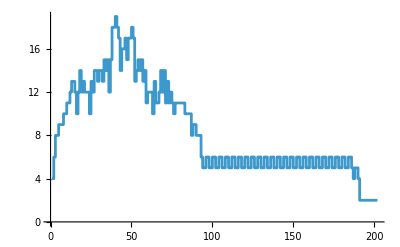

```mathematica
ListStepPlot[Length/@FLZCEncode/@CellularAutomaton[l1[[bmi[[1]], 1]],{{1}, 0},{200, {-25, 25}}]]
```

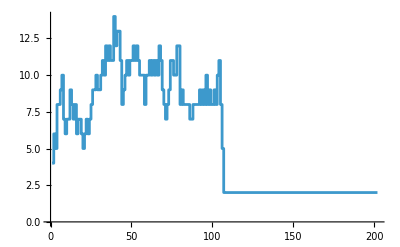
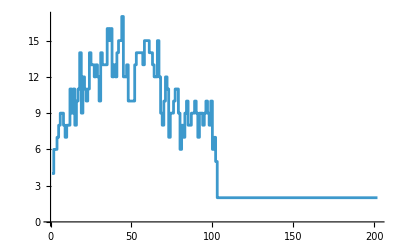
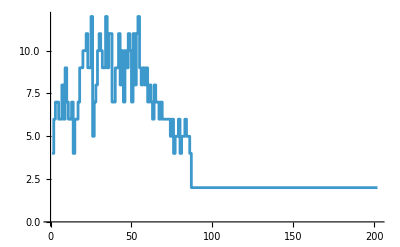
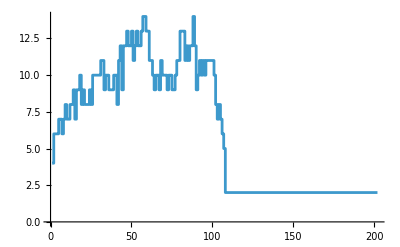
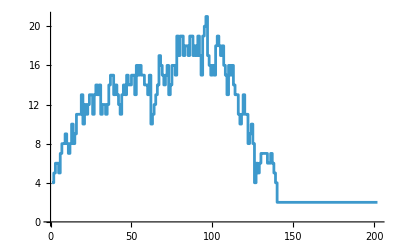
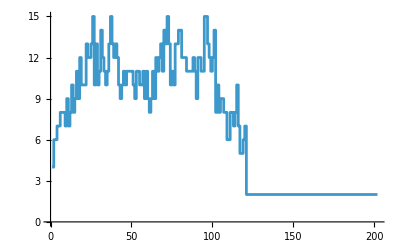
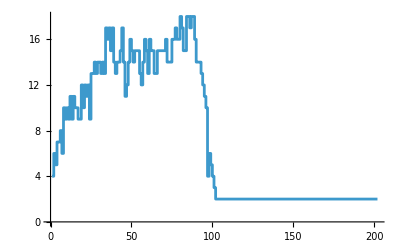
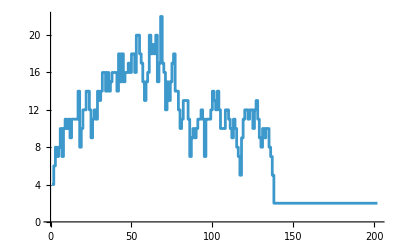
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListStepPlot[Length/@FLZCEncode/@CellularAutomaton[#,{{1}, 0},{200, {-25, 25}}]]&/@ l1[[bmi[[1;;10]], 1]]
```

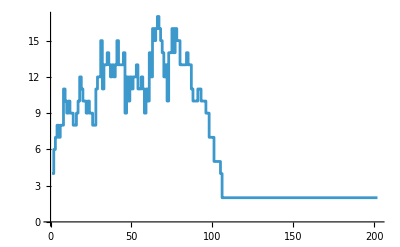
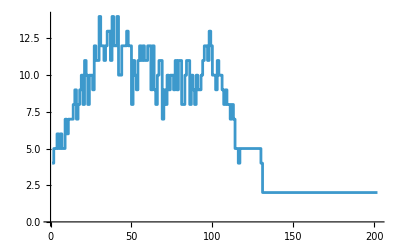
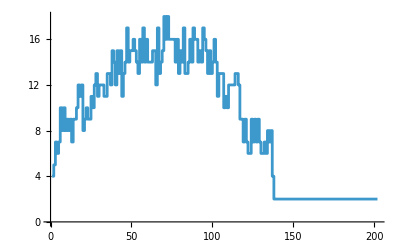
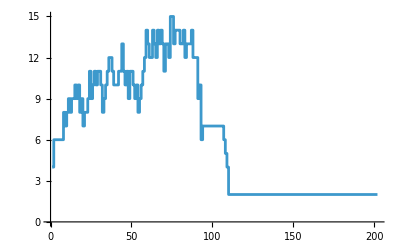
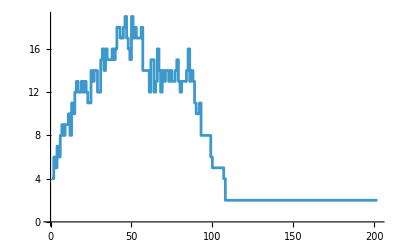
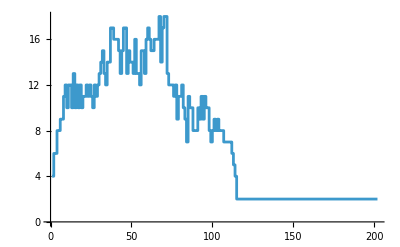
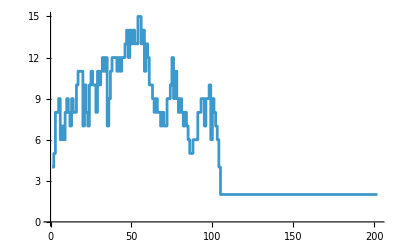
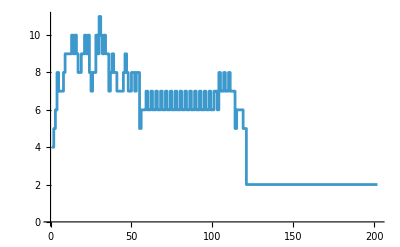

```mathematica
ListStepPlot[Length/@FLZCEncode/@CellularAutomaton[#,{{1}, 0},{200, {-25, 25}}]]&/@ {{{329544069266708592463225775856558462236,4,1},105},{{31454797907058801713769223942564501248,4,1},113},{{94341792732834871885391301103528730764,4,1},118},{{313250599264395119456857147759593994508,4,1},108},{{259935089950547344012002055302160592200,4,1},102},{{247714077771917130081980187654439082376,4,1},110},{{297274882967345950128571968445382186124,4,1},104},{{179079137400185473786391819702541282316,4,1},111},{{163313090342284595938913846502066693128,4,1},128},{{25359040487030105047738027699989445448,4,1},124},{{276033802575773574714948886195065539400,4,1},115},{{203604439604841868193116868463062121272,4,1},109},{{238281312689748660330223481542815453752,4,1},113},{{134345922194069195773321304398798272016,4,1},100},{{158194304512403226430615670631995011596,4,1},101},{{272480688721516524826602064283746072588,4,1},123},{{268421576596783154125046530204266236812,4,1},111},{{252507139021300249072588345221334974732,4,1},107},{{113554917644982243172837530688048101952,4,1},103},{{72931379031802397861345927583448738624,4,1},104}}[[All, 1]]
```

```mathematica
Style[Row[Riffle[{{"[◼]", "PlotCA"}}[CellularAutomaton[First[#],{{1},0},{150,{-100,100}}],ImageSize->{Automatic,250}]&/@{{{329544069266708592463225775856558462236,4,1},105},{{31454797907058801713769223942564501248,4,1},113},{{94341792732834871885391301103528730764,4,1},118},{{313250599264395119456857147759593994508,4,1},108},{{259935089950547344012002055302160592200,4,1},102},{{247714077771917130081980187654439082376,4,1},110},{{297274882967345950128571968445382186124,4,1},104},{{179079137400185473786391819702541282316,4,1},111},{{163313090342284595938913846502066693128,4,1},128},{{25359040487030105047738027699989445448,4,1},124},{{276033802575773574714948886195065539400,4,1},115},{{203604439604841868193116868463062121272,4,1},109},{{238281312689748660330223481542815453752,4,1},113},{{134345922194069195773321304398798272016,4,1},100},{{158194304512403226430615670631995011596,4,1},101},{{272480688721516524826602064283746072588,4,1},123},{{268421576596783154125046530204266236812,4,1},111},{{252507139021300249072588345221334974732,4,1},107},{{113554917644982243172837530688048101952,4,1},103},{{72931379031802397861345927583448738624,4,1},104}},Spacer[4]]],LineSpacing->{1.05,1.1}]
```